```mathematica
Manipulate[ParametricPlot[{Cos[t],A*Cos[ω*t+ϕ*Pi]},{t,0,10},PlotRange->{-1.1,1.1}],{ω,1,10},{ϕ,0,10},{A,0.1,1}]
```

```mathematica
Manipulate[Plot[{Cos[ω1*t-(ω1/v1)*x+ϕ]+Cos[ω2*t-(ω2/v2)*x]},{x,0,30},PlotRange->{{0,30},{-2,2}},AspectRatio->1/5],{ω1,0,5},{ω2,0,5},{v1,-5,5},{v2,-5,5},{ϕ,0,2*Pi},{t,0,60}]
```

```mathematica
1+D[Cos[t]Sin[x],x]
```

```mathematica
1+Cos[t] Cos[x]
```

```mathematica
Clear[x,t,i,j,table,t0,ft]
t0={};
table=Table[i-0.4Cos[t]Sin[i]-j*(i-0.4Cos[t]Sin[i]),{i,0,4Pi,Pi/16},{j,0,1}];
Do[Part[table,All,2]=k;t0=Append[t0,table],{k,-1,1,0.2}];
With[{t0=Flatten[t0,1]},Manipulate[
Show[
Plot[{0.6Cos[t]Sin[x],1+0.2Cos[t]Cos[x]},{x,0,4Pi},
PlotRange->{-2,3}],

DensityPlot[Log[2+0.2Cos[t]Cos[x]],{x,0,4Pi},{y,1.5,2.5},
ColorFunction->"TemperatureMap",
ColorFunctionScaling->False,PlotPoints->50],

Graphics[Point[t0]]],

{t,0,4Pi}]]
```

```mathematica
Clear[x,t,i,j,table,tt]
```

{}

{{1,0},{2,0},{3,0},{4,0},{5,0}}

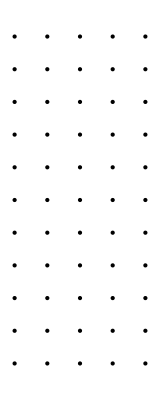

```mathematica
t0={}
tt=Table[i-j*(i),{i,5},{j,0,1}]
For[k=-6,k≤4,k++;Part[tt,All,2]=k;t0=Append[t0,tt]]
Graphics[Point[Flatten[t0,1]]]
table=Table[i-0.6Cos[t]Sin[i]-j*(i-0.6Cos[t]Sin[i]),{i,0,4Pi,Pi/16},{j,0,1}];
For[k=-6,k≤4,k++;Part[table,All,2]=k;t0=Append[t0,table]];
Graphics[Point[Flatten[t0,1]]]
```

```mathematica
Table[i,{i,-5,5}]
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

```mathematica
tt=Table[i-j*(i),{i,5},{j,0,1}]
```

{{1,0},{2,0},{3,0},{4,0},{5,0}}

```mathematica
Clear[x,t,i,j,table,t0]
t0={};
table=Table[i-0.4Cos[t]Sin[i]-j*(i-0.4Cos[t]Sin[i]),{i,0,4Pi,Pi/16},{j,0,1}];
Do[Part[table,All,2]=k;t0=Append[t0,table],{k,-1,1,0.2}];
t0
```